```mathematica
Integrate[Exp[-t/τ]*(A*Sin[t*ω]^2+B),{t,0,Infinity}]
```

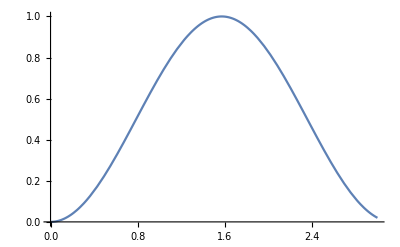

```mathematica
Plot[Sin[x]^2,{x,0,3}]
```

```mathematica
m=1
```

1

```mathematica
Plot[(2 m^2)/((1/g)^3+4 (1/g) m^2),{g,0,0.4}]
```

-Graphics-

```mathematica
ContourPlot3D[(2 m^2)/(g^3+4 g m^2),{g,0,10},{m,0,10}]
```

ContourPlot3D::argrx: ContourPlot3D called with 3 arguments; 4 arguments are expected.

ContourPlot3D[(2 m^2)/(g^3+4 g m^2),{g,0,10},{m,0,10}]

```mathematica
Solve[(2 m^2)/(g^3+4 g m^2) ==Exp[-x*g]*Sin[x*m]^2 , x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

```mathematica
NSolve[(2 m^2)/(g^3+4 g m^2)==ⅇ^(-g x) Sin[m x]^2,x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[(2 m^2)/(g^3+4 g m^2)==ⅇ^(-g x) Sin[m x]^2,x]

```mathematica
++
```

```mathematica
Clear[A,B,ω]
```

```mathematica
Integrate[Exp[-t/τ]/τ*(A*Sin[t*ω]^2+B),{t,0,Infinity}]
```

ConditionalExpression[B+(2 A τ^2 ω^2)/(1+4 τ^2 ω^2),Re[1/τ]>2 Abs[Im[ω]]]

```mathematica
B=0; A= 1; ω = 214198.036115241855;
```

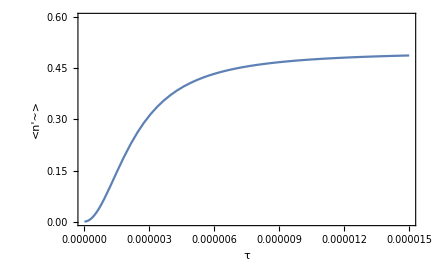

```mathematica
Plot[B+(2 A τ^2 ω^2)/(1+4 τ^2 ω^2),{τ,0,15*10^-6}, PlotRange->{Automatic, {0,0.6}}, Frame -> True,FrameStyle -> Black,FrameLabel-> {"τ","<n'~>"}]
```

```mathematica
ts = Table[{τ,t /. NSolve[B+(2 A τ^2 ω^2)/(1+4 τ^2 ω^2) == (A*Sin[t*ω]^2+B),t][[2]]},{τ,10^-7,5*10^-6,10^-7}]
```

```mathematica
Total[ts]
```

{51/400000,ConditionalExpression[1.×10^-6 (0.139123+6.28319 C[1])+1.×10^-6 (0.265729+6.28319 C[1])+1.×10^-6 (0.372348+6.28319 C[1])+1.×10^-6 (0.457522+6.28319 C[1])+1.×10^-6 (0.523599+6.28319 C[1])+1.×10^-6 (0.574261+6.28319 C[1])+1.×10^-6 (0.613089+6.28319 C[1])+1.×10^-6 (0.643033+6.28319 C[1])+1.×10^-6 (0.666352+6.28319 C[1])+1.×10^-6 (0.684719+6.28319 C[1])+1.×10^-6 (0.699358+6.28319 C[1])+1.×10^-6 (0.711161+6.28319 C[1])+1.×10^-6 (0.720785+6.28319 C[1])+1.×10^-6 (0.728716+6.28319 C[1])+1.×10^-6 (0.735314+6.28319 C[1])+1.×10^-6 (0.740855+6.28319 C[1])+1.×10^-6 (0.745547+6.28319 C[1])+1.×10^-6 (0.749551+6.28319 C[1])+1.×10^-6 (0.752992+6.28319 C[1])+1.×10^-6 (0.755969+6.28319 C[1])+1.×10^-6 (0.758561+6.28319 C[1])+1.×10^-6 (0.76083+6.28319 C[1])+1.×10^-6 (0.762827+6.28319 C[1])+1.×10^-6 (0.764593+6.28319 C[1])+1.×10^-6 (0.766163+6.28319 C[1])+1.×10^-6 (0.767563+6.28319 C[1])+1.×10^-6 (0.768817+6.28319 C[1])+1.×10^-6 (0.769945+6.28319 C[1])+1.×10^-6 (0.770962+6.28319 C[1])+1.×10^-6 (0.771883+6.28319 C[1])+1.×10^-6 (0.772719+6.28319 C[1])+1.×10^-6 (0.773481+6.28319 C[1])+1.×10^-6 (0.774176+6.28319 C[1])+1.×10^-6 (0.774813+6.28319 C[1])+1.×10^-6 (0.775397+6.28319 C[1])+1.×10^-6 (0.775935+6.28319 C[1])+1.×10^-6 (0.776431+6.28319 C[1])+1.×10^-6 (0.776889+6.28319 C[1])+1.×10^-6 (0.777312+6.28319 C[1])+1.×10^-6 (0.777706+6.28319 C[1])+1.×10^-6 (0.778071+6.28319 C[1])+1.×10^-6 (0.778411+6.28319 C[1])+1.×10^-6 (0.778728+6.28319 C[1])+1.×10^-6 (0.779024+6.28319 C[1])+1.×10^-6 (0.7793+6.28319 C[1])+1.×10^-6 (0.77956+6.28319 C[1])+1.×10^-6 (0.779803+6.28319 C[1])+1.×10^-6 (0.780031+6.28319 C[1])+1.×10^-6 (0.780246+6.28319 C[1])+1.×10^-6 (0.780448+6.28319 C[1]),C[1]∈Integers]}

```mathematica
ω =1;
```

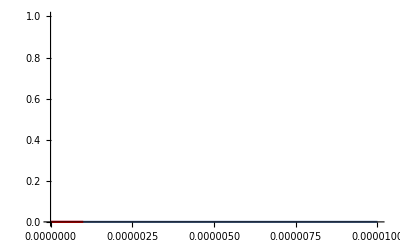

```mathematica
Show[{ListPlot[ts, PlotRange->{{0,10^-5},{0,1}}],Plot[(Pi/4)(1-Exp[-1.9x]),{x,0,10^-5}],Plot[(√2 τ)/(√(1+4 τ^2 ω^2)),{τ,0,10^-6},PlotStyle -> Red]},PlotRange->{{0,10^-5},{0,1}}]
```

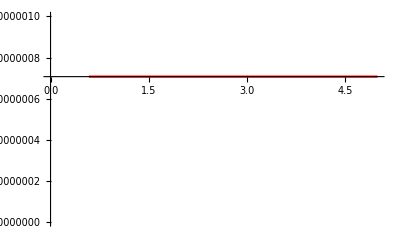

```mathematica
Show[{Plot[(√2 τ)/(√(1+4 τ^2 ω^2)),{τ,0,5},PlotStyle -> Red]},PlotRange->{{0,5},{0,10^-6}}]
```

```mathematica
Series[Sin[t*ω]^2,{t,0,4}]
```

ω^2 t^2-(ω^4 t^4)/3+O[t]^5

```mathematica
Clear[ω]
```

```mathematica
Solve[B+(2 A τ^2 ω^2)/(1+4 τ^2 ω^2) == (A*(ω^2 t^2)+B),t]
```

{{t→-(√2 τ)/(√(1+4 τ^2 ω^2))},{t→(√2 τ)/(√(1+4 τ^2 ω^2))}}

```mathematica
Plot[(√(3/ω^2+(√3 √(3+4 τ^2 ω^2))/(ω^2 √(1+4 τ^2 ω^2))))/(√2),]
```

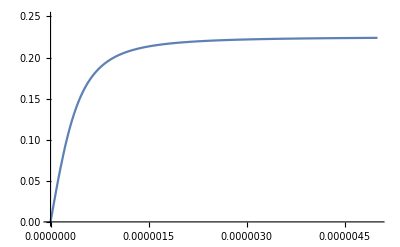

```mathematica
Plot[((√2 τ)/(√(1+4 τ^2 ω^2)))/(Pi/ω),{τ,0,5*10^-6}, PlotRange->{Automatic, {0,0.25}}]
```

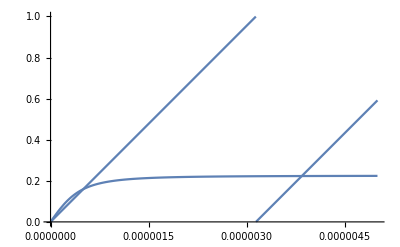

```mathematica
Show[{Plot[((√2 τ)/(√(1+4 τ^2 ω^2)))/(Pi/ω),{τ,0,5*10^-6}, PlotRange->{Automatic, {0,1}}],Plot[Mod[τ,(Pi/ω)]/(Pi/ω),{τ,0,5*10^-6}]}]
```

```mathematica
Mod[2,2]
```

0

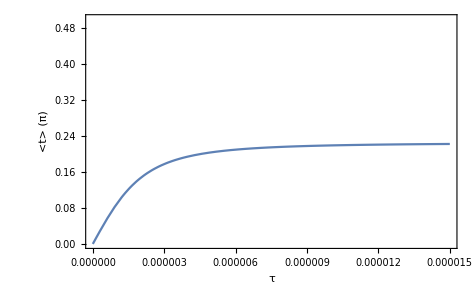

```mathematica
Plot[((√2 τ)/(√(1+4 τ^2 ω^2)))/(Pi/ω),{τ,0,15*10^-6}, PlotRange->{Automatic, {0,0.5}},Frame -> True,FrameStyle -> Black,FrameLabel-> {"τ","<t> (π)"}]
```